```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
$Assumptions={n}∈Integers ∧n>0
```

n∈Integers&&n>0

# Mathematica for Engineering Systems: Part III

## Introduction

Part III continues with Discrete-time system, first difference equations,  and second discrete-time Fourier Transform.

Difference Equations

### Intro

The equivalence of differential equations in the discrete time domain are difference equations, relating output values at a time (n Δt) to input samples and previous (for causal systems) output values.

### The function Fourier for the Discrete Fourier Transform

```mathematica
(*Write down the h and take its DTFT*)
Clear[n,w]
h=1/4 DiscreteDelta[n+1]+1/2 DiscreteDelta[n]+1/4 DiscreteDelta[n-1];
hTransformed=FourierSequenceTransform[h,n,w]
```

1/4 ⅇ^(-ⅈ w) (1+ⅇ^(ⅈ w))^2

```mathematica
x=1 DiscreteDelta[n]+2 DiscreteDelta[n-1]-2 DiscreteDelta[n-2]+DiscreteDelta[n-3]+4 DiscreteDelta[n-4]-DiscreteDelta[n-5]+DiscreteDelta[n-6]+2 DiscreteDelta[n-7];
xTransformed=FourierSequenceTransform[x,n,w]
```

ⅇ^(-7 ⅈ w) (2+ⅇ^(ⅈ w)-ⅇ^(2 ⅈ w)+4 ⅇ^(3 ⅈ w)+ⅇ^(4 ⅈ w)-2 ⅇ^(5 ⅈ w)+2 ⅇ^(6 ⅈ w)+ⅇ^(7 ⅈ w))

```mathematica
z=InverseFourierSequenceTransform[xTransformed hTransformed,w,n]
```

Piecewise[{{-1/4, n==2}, {1/4, n==-1}, {1/2, n==8}, {3/4, n==1||n==5||n==6}, {1, n==0||n==3}, {5/4, n==7}, {2, n==4}, {0, True}}]

```mathematica
N@InverseFourierSequenceTransform[xTransformed hTransformed hTransformed,w,n]
```

Piecewise[{{0.0625, n==-2.}, {0.125, n==9.}, {0.3125, n==2.}, {0.375, n==-1.}, {0.5625, n==1.||n==8.}, {0.75, n==0.}, {0.875, n==6.}, {0.9375, n==3.||n==7.}, {1.0625, n==5.}, {1.4375, n==4.}, {0., True}}]

### Discrete State-Space Model

```mathematica
ss2=StateSpaceModel[{{{0,1,0,0},{-0.1,-0.001,0.1,0.001},{0,0,0,1}, {0.05,0.005,-0.5,-0.005}},{{0},{0},{0},{1}},{{1,0,0,0 }}}, SamplingPeriod->0.1]
```

01000-0.1-0.0010.10.0010000100.050.005-0.5-0.0051100000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

FIR-Filters

```mathematica
t=Table[{x,UnitBox[x/(0.9 π)]},{x,0,3,2π/11}]
```

{{0,1},{(2 π)/11,1},{(4 π)/11,1},{(6 π)/11,0},{(8 π)/11,0},{(10 π)/11,0}}

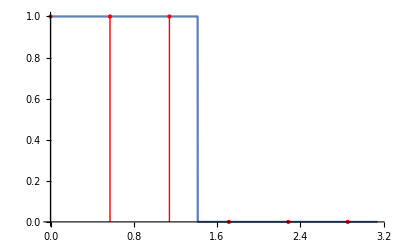

```mathematica
Show[{Plot[UnitBox[x/(0.9 π)],{x,0,π},Exclusions->None],ListPlot[t,PlotRange->All,PlotStyle->{Red,PointSize[Large]},Filling->0,FillingStyle->Red]}]
```

```mathematica
{frequencies,amplitudes}=Transpose[t];
FrequencySamplingFilterKernel[amplitudes,1]
```

{0.069411,-0.0540319,-0.10942,0.0473735,0.319394,0.454545,0.319394,0.0473735,-0.10942,-0.0540319,0.069411}

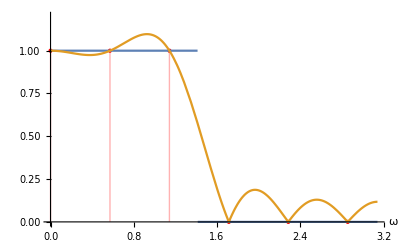

```mathematica
Show[{ListPlot[t,PlotRange->{{0,π},{0,1.2}},PlotStyle->{Red,PointSize[Medium]},Filling->Axis,AxesLabel->{ω,None}],Plot[{UnitBox[ω/(0.9 π)],Evaluate[Abs[ListFourierSequenceTransform[FrequencySamplingFilterKernel[amplitudes,1],ω]]]},{ω,0,π},PlotRange->{{0,π},All}]}]
```

Continuous-time ↔ Discrete-time

```mathematica
tfc=TransferFunctionModel[(s+1)/(s^2+1 s+1),s]
```

(1+s)/(1+s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
tfd=ToDiscreteTimeModel[tfc,0.1,z,Method->"ZeroOrderHold"]
```

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

ToDiscreteTimeModel[(1+s)/(1+s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,0.1,0,Method→ZeroOrderHold]

```mathematica
{gm,pm}=GainPhaseMargins[tfd]
```

GainPhaseMargins::invsys2: Method→ZeroOrderHold is not a valid TransferFunctionModel, or StateSpaceModel.

Set::shape: Lists {gm,pm} and GainPhaseMargins[ToDiscreteTimeModel[1/1,0.1,0,Method→ZeroOrderHold]] are not the same shape.

GainPhaseMargins::invsys2: Method→ZeroOrderHold is not a valid TransferFunctionModel, or StateSpaceModel.

GainPhaseMargins[ToDiscreteTimeModel[(1+s)/(1+s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,0.1,0,Method→ZeroOrderHold]]

```mathematica
max=100;
yn=OutputResponse[tfd,Table[UnitStep[n],{n,0,max}]];
ListPlot[yn,Joined->True,InterpolationOrder->0,PlotRange->{{0,max},{0,1.4}},Frame->True,FrameLabel->{{"y[n]",None},{"n","unit step response"}},ImageSize->400,AspectRatio->1,BaseStyle->14]
```

OutputResponse::invsys: ToDiscreteTimeModel[1/1,0.1,0,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

OutputResponse::invsys: ToDiscreteTimeModel[1./1.,0.1,0,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ToDiscreteTimeModel::ivar: 0. is not a valid variable.

OutputResponse::invsys: ToDiscreteTimeModel[1./1.,0.1,0.,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

General::stop: Further output of ToDiscreteTimeModel::ivar will be suppressed during this calculation.

OutputResponse::invsys: ToDiscreteTimeModel[1./1.,0.1,0,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

General::stop: Further output of OutputResponse::invsys will be suppressed during this calculation.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[OutputResponse[ToDiscreteTimeModel[(1+s)/(1+s+s^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic,0.1,0,Method→ZeroOrderHold],{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}],Joined→True,InterpolationOrder→0,PlotRange→{{0,100},{0,1.4}},Frame→True,FrameLabel→{{y[n],None},{n,unit step response}},ImageSize→400,AspectRatio→1,BaseStyle→14]

z-Transform

```mathematica
ZTransform[UnitStep[n],n,z]
```

ZTransform[1,12,0]

### Inverse z-Transform

```mathematica
x[n_]:=InverseZTransform[z/(z-1),z,n]
```

SetDelayed::write: Tag Integer in 0[n_] is Protected.

$Failed

```mathematica
ListPlot[Table[{n,x[n]},{n,0,10}],Frame->True,FrameLabel->{{"x[n]",None},{"n","Inverse Ztransform of z/(z-1)"}},FormatType->StandardForm,RotateLabel->False,Filling->Axis,FillingStyle->Red,PlotRange->{Automatic,{0,1.3}},PlotMarkers->{Automatic,12}]
```

-Graphics-

### Expanded example

```mathematica
nSamples=14;
f=1.0;
sampleTime=1/f;
u[t_]:=Sin[2*Pi*(f/3)*t]*Exp[-0.3*t]
ud[n_]:=u[n*sampleTime];
plant=TransferFunctionModel[(3 s)/((s+1)(s+2)),s];
sysd=ToDiscreteTimeModel[plant,sampleTime,z,Method->"ZeroOrderHold"]
```

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

ToDiscreteTimeModel[(3 s)/((1+s) (2+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11311FalseFalseFalseAutomaticNoneAutomatic,1.,0,Method→ZeroOrderHold]

OutputResponse::invsys: ToDiscreteTimeModel[3/(,1.,0,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

OutputResponse::invsys: ToDiscreteTimeModel[3./(,1.,0,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

ToDiscreteTimeModel::ivar: 0. is not a valid variable.

OutputResponse::invsys: ToDiscreteTimeModel[3./(,1.,0.,Method→ZeroOrderHold] is not a valid TransferFunctionModel, StateSpaceModel, AffineStateSpaceModel, or NonlinearStateSpaceModel.

General::stop: Further output of OutputResponse::invsys will be suppressed during this calculation.

ListPlot::lpn: OutputResponse[ToDiscreteTimeModel[3./(,1.,0.,Method→ZeroOrderHold],{0.,0.641567,-0.475285,-9.95808×10^-17,0.260842,-0.193236,-8.09731×10^-17,0.10605,-0.0785641,-4.93818×10^-17,0.0431169,-0.0319418,-2.67695×10^-17,0.01753,-0.0129866}] is not a list of numbers or pairs of numbers.

ToDiscreteTimeModel::ivar: 0 is not a valid variable.

General::stop: Further output of ToDiscreteTimeModel::ivar will be suppressed during this calculation.

ListPlot::lpn: OutputResponse[ToDiscreteTimeModel[3./(,1.,0.,Method→ZeroOrderHold],{0.,0.641567,-0.475285,-9.95808×10^-17,0.260842,-0.193236,-8.09731×10^-17,0.10605,-0.0785641,-4.93818×10^-17,0.0431169,-0.0319418,-2.67695×10^-17,0.01753,-0.0129866}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

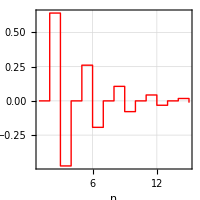
-Graphics- | ListPlot[OutputResponse[ToDiscreteTimeModel[(3 s)/((1+s) (2+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11311FalseFalseFalseAutomaticNoneAutomatic,1.,0,Method→ZeroOrderHold],{0.,0.641567,-0.475285,-9.95808×10^-17,0.260842,-0.193236,-8.09731×10^-17,0.10605,-0.0785641,-4.93818×10^-17,0.0431169,-0.0319418,-2.67695×10^-17,0.01753,-0.0129866}],{Joined→True,PlotRange→All,AspectRatio→1,InterpolationOrder→0,ImageSize→200,Frame→True,PlotRange→{{0,14},{-0.5,0.5}},GridLines→Automatic,GridLinesStyle→Dashing[{Small,Small}]},FrameLabel→{{y(t),None},{n,plant output y(nT)}},PlotStyle→{Thickness[Large],RGBColor[0, 0, 1]}]

```mathematica
opts={Joined->True,PlotRange->All,AspectRatio->1,InterpolationOrder->0,ImageSize->200,Frame->True,PlotRange->{{0,nSamples},{-0.5,0.5}},GridLines->Automatic,GridLinesStyle->Dashed};
inputPlot=ListPlot[Table[ud[k],{k,0,nSamples}],Evaluate[opts],FrameLabel->{{"u(t)",None},{"n","plant input u(nT)"}},PlotStyle->{Thick,Red}];
plantPlot=ListPlot[OutputResponse[sysd,Table[ud[k],{k,0,nSamples}]],Evaluate[opts],FrameLabel->{{"y(t)",None},{"n","plant output y(nT)"}},PlotStyle->{Thick,Blue}];
Grid[{{inputPlot,plantPlot}}]
```

```mathematica
Show[{inputPlot,plantPlot},PlotLabel->"input/output plot"]
```

Show::gcomb: Could not combine the graphics objects in Show[{,ListPlot[OutputResponse[ToDiscreteTimeModel[TransferFunctionModel[{{«1»},Times[«2»]},s],1.,0,Method→ZeroOrderHold],{0.,0.641567,-0.475285,-9.95808×10^-17,0.260842,-0.193236,-8.09731×10^-17,«20»,-«20»,-4.93818×10^-17,0.0431169,-0.0319418,-2.67695×10^-17,0.01753,-0.0129866}],«2»,PlotStyle→«1»]},«1»].

Show[{-Graphics-,ListPlot[OutputResponse[ToDiscreteTimeModel[(3 s)/((1+s) (2+s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11311FalseFalseFalseAutomaticNoneAutomatic,1.,0,Method→ZeroOrderHold],{0.,0.641567,-0.475285,-9.95808×10^-17,0.260842,-0.193236,-8.09731×10^-17,0.10605,-0.0785641,-4.93818×10^-17,0.0431169,-0.0319418,-2.67695×10^-17,0.01753,-0.0129866}],{Joined→True,PlotRange→All,AspectRatio→1,InterpolationOrder→0,ImageSize→200,Frame→True,PlotRange→{{0,14},{-0.5,0.5}},GridLines→Automatic,GridLinesStyle→Dashing[{Small,Small}]},FrameLabel→{{y(t),None},{n,plant output y(nT)}},PlotStyle→{Thickness[Large],RGBColor[0, 0, 1]}]},PlotLabel→input/output plot]

IIR-Filters